```mathematica
data={{280,770},{284,800},{292,840},{295,810},{298,735},{305,640},{308,390},{315,560}}
```

{{280,770},{284,800},{292,840},{295,810},{298,735},{305,640},{308,390},{315,560}}

```mathematica
Transpose[data][[2]]
```

```mathematica
model=NonlinearModelFit[data,a+b*x+c*x^2,{a,b,c},x]
```

FittedModel[-24496.3+179.611 x-0.318723 x^2]

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -24496.3 | 28736.3 | -0.85245 | 0.43289
b | 179.611 | 193.59 | 0.927791 | 0.396097
c | -0.318723 | 0.325688 | -0.978615 | 0.372714

```mathematica
MatrixForm[model["CovarianceMatrix"]]
```

(8.25777×10^8 | -5.56218×10^6 | 9353.11
-5.56218×10^6 | 37477.2 | -63.0401
9353.11 | -63.0401 | 0.106073)

```mathematica
residuals=model["FitResiduals"]
```

{-37.0217,-6.42781,65.3575,57.7949,10.9692,4.02009,-198.682,103.99}

```mathematica
ListPlot[Table[{data[[i]][[1]],residuals[[i]]},{i,1,6}],PlotRange->Automatic]
```

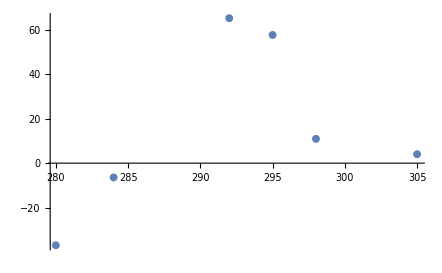
```mathematica
-Graphics-
model["ParameterConfidenceIntervals",ConfidenceLevel->.9]
```

-Graphics-

{{-82401.4,33408.8},{-210.483,569.705},{-0.975001,0.337554}}

```mathematica
model["ParameterPredictionIntervals",ConfidenceLevel->.9]
```